# Plotting projected (electronic) DOS from different DFT codes

The notebook can read PDOS from different DFT codes (Fireball, VASP, GPAW, FHI-AIMS) and plot them in the same way.
In the second part (VIEW) there is possibility to visualize the amount of PDOS per atom in 3D balls & sticks model.

```mathematica
(* a way to lower down the amount of memory *)
$HistoryLength=2;
```

```mathematica
(* for path checking *)
atomicprop=Import[NotebookDirectory[]<>"/atomic_prop.dat","Table"];
path="~//Documents/WORK/z-sshfs/Tarkil/TlSi/VASP_collinear/";
geom=(*Import[path<>"CONTCAR","Table"];*) (*Not necessary, working for Fireball only *)  (*Import[path<>"geometry.in","Table"];*)(*Not necessary, working for FHI-AIMS only *)
(*maxat1=geom[[1,1]]*) (* This is not neccessary for plotting *)
geom[[Range[1,20],All]]//TableForm  (* Just to show sample*)
```

# |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
# | This | is | the | geometry | file | that | corresponds | to | the | current | relaxation | step. |  |  |  | 
# | If | you | do | not | want | this | file | to | be | written, | set | the | write_restart_geometry | flag | to | .false.
# | aims_uuid | : | DF1F1D00-BD73-4BC4-A92D-812BE300E03E |  |  |  |  |  |  |  |  |  |  |  |  | 
# |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
atom | 0.0283837 | 0.0218911 | 0.0422106 | Fe |  |  |  |  |  |  |  |  |  |  |  | 
atom | 2.40769 | 2.39652 | 0.0449828 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | 2.40331 | -2.35766 | 0.0395522 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | -2.35088 | -2.35278 | 0.0398045 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | -2.34655 | 2.40142 | 0.0448143 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | 1.97641 | 0.0198198 | 0.0419272 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | 2.78136 | -1.09431 | 0.0406864 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 2.78356 | 1.13269 | 0.0432971 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 4.17396 | -0.682082 | 0.040904 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 4.17514 | 0.717959 | 0.0424902 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 5.36216 | -1.40443 | 0.0401646 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 5.3644 | 1.43861 | 0.0433851 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 6.55088 | -0.685807 | 0.0411359 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 6.55201 | 0.71824 | 0.0427021 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 5.35027 | -2.48424 | 0.039025 | H |  |  |  |  |  |  |  |  |  |  |  |

## Fireball inputs

```mathematica
shift=0.0

list=(*{1,2,3,4,5,6,7,8,9,10,(*11,12,*)13,14,15,16,17};*)Table[i,{i,1,12(*maxat1*),1}];
path0=path (*"~/ ... /"*);
dos1=Import[path0<>"dens_0001.dat","Table"][[All,{1,2}]];dos1[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"dens_0"<>ToString[i]<>".dat","Table"],If[i<10,Import[path0<>"dens_000"<>ToString[i]<>".dat","Table"],Import[path0<>"dens_00"<>ToString[i]<>".dat","Table"]]]},{i,list}];dos1[[All,2]]=Sum[dd[i][[All,Dimensions[dd[i]][[2]]-1]],{i,list}];Do[{dd[i]=.},{i,list}];f=Import[path0<>"fermi.dat","Table"][[1,4]];dos1=Inner[Times,Inner[Plus,dos1,{-f+shift,0},List],{1,1(*/Length[list]*)},List];f=.;

list=(*{18,19,20,21,22,23,36,37,38,39,40,41,42,24,45,27,44,26,47,29,48,49,50,51,52,53,30,31,32,33,34,35};*)Table[i,{i,1,12(*maxat1*),1}];
path0="~/Documents/WORK/z-sshfs/Tarkil/AC_7x7/8_layers_clean/";
dos2=Import[path0<>"dens_0001.dat","Table"][[All,{1,2}]];dos2[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"dens_0"<>ToString[i]<>".dat","Table"],If[i<10,Import[path0<>"dens_000"<>ToString[i]<>".dat","Table"],Import[path0<>"dens_00"<>ToString[i]<>".dat","Table"]]]},{i,list}];dos2[[All,2]]=Sum[dd[i][[All,Dimensions[dd[i]][[2]]-1]],{i,list}];Do[{dd[i]=.},{i,list}];f=Import[path0<>"fermi.dat","Table"][[1,4]];
dos2=Inner[Times,Inner[Plus,dos2,{-f+shift,0},List],{1,1(*/Length[list]*)},List];f=.;

(*list=(*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17};*)Table[i,{i,1,61,1}];
path0="~/ ... /";
dos3=Import[path0<>"dens_TOT.dat","Table"][[All,{1,2}]];dos3[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"dens_0"<>ToString[i]<>".dat","Table"],If[i<10,Import[path0<>"dens_000"<>ToString[i]<>".dat","Table"],Import[path0<>"dens_00"<>ToString[i]<>".dat","Table"]]]},{i,list}];dos3[[All,2]]=Sum[dd[i][[All,Dimensions[dd[i]][[2]]-1]],{i,list}];Do[{dd[i]=.},{i,list}];f=Import[path0<>"fermi.dat","Table"][[1,4]];
dos3=Inner[Times,Inner[Plus,dos3,{-f+shift,0},List],{1,1(*/Length[list]*)},List];f=.;*)

(*list=(*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17};*)Table[i,{i,1,61,1}];
path0="~/ ... /";
dos4=Import[path0<>"dens_TOT.dat","Table"][[All,{1,2}]];dos4[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"dens_0"<>ToString[i]<>".dat","Table"],If[i<10,Import[path0<>"dens_000"<>ToString[i]<>".dat","Table"],Import[path0<>"dens_00"<>ToString[i]<>".dat","Table"]]]},{i,list}];dos4[[All,2]]=Sum[dd[i][[All,Dimensions[dd[i]][[2]]-1]],{i,list}];Do[{dd[i]=.},{i,list}];f=Import[path0<>"fermi.dat","Table"][[1,4]];
dos4=Inner[Times,Inner[Plus,dos4,{-f+shift,0},List],{1,1(*/Length[list]*)},List];f=.;*)

(*list={1,2,3,4,5,(*6,*)7,8,9,10,11,12,13,14,15,16,17};
path0="~/ ... /";
dos5=Import[path0<>"dens_TOT.dat","Table"][[All,{1,2}]];dos5[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"dens_0"<>ToString[i]<>".dat","Table"],If[i<10,Import[path0<>"dens_000"<>ToString[i]<>".dat","Table"],Import[path0<>"dens_00"<>ToString[i]<>".dat","Table"]]]},{i,list}];dos5[[All,2]]=Sum[dd[i][[All,Dimensions[dd[i]][[2]]-1]],{i,list}];Do[{dd[i]=.},{i,list}];f=Import[path0<>"fermi.dat","Table"][[1,4]];
dos5=Inner[Times,Inner[Plus,dos5,{-f+shift,0},List],{1,1(*/Length[list]*)},List];f=.;*)

(*list={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16(*,17*)};
path0="~/ ... /";
dos6=Import[path0<>"dens_TOT.dat","Table"][[All,{1,2}]];dos6[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"dens_0"<>ToString[i]<>".dat","Table"],If[i<10,Import[path0<>"dens_000"<>ToString[i]<>".dat","Table"],Import[path0<>"dens_00"<>ToString[i]<>".dat","Table"]]]},{i,list}];dos6[[All,2]]=Sum[dd[i][[All,Dimensions[dd[i]][[2]]-1]],{i,list}];Do[{dd[i]=.},{i,list}];f=Import[path0<>"fermi.dat","Table"][[1,4]];
dos6=Inner[Times,Inner[Plus,dos6,{-f+shift,0},List],{1,1(*/Length[list]*)},List];f=.;*)
```

0.

## VASP inputs

```mathematica
list=(*{1,2,3,4}*)Table[i,{i,1,12,1}];
pathse="~/Documents/WORK/z-sshfs/Luna/CuPc_SiSn_rep/VASP_4l_substrate/1Si_SnSi/no_spin/"
doscar1=Import[pathse<>"DOSCAR","Table"];
doscar1[[Range[1,7]]];
noat=doscar1[[1,1]];
nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];
fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
For[i=1,i≤noat,i++,{doses[i]=Transpose[{dos01[i].{1,0,0,0},dos01[i].{0,1,1,1}}],dos01[i]=.}]; (* spd division only LORBIT=10 *)
(*For[i=1,i≤noat,i++,{doses[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,1,1,1,1,1,1,1,1}}],dos01[i]=.}];*) (* spxpy.. division LORBIT=11 *)
dosesmol=Array[Null,{nosteps,2}];
dosesmol[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmol[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmol[[i,2]]=dosesmol[[i,2]]+doses[list[[j]]][[i,2]]]}];
(*fermi=Import[pathse<>"fermi.dat"][[1,3]]*)
dosesmol2=Inner[Plus,dosesmol,{-fermi,0},List];

dos1 = dosesmol2; dosesmol=.;dosesmol2=.;

list=(*{1,2,3,4}*)Table[i,{i,1,12,1}];
pathse="~/Documents/WORK/z-sshfs/Luna/CuPc_SiSn_rep/VASP_4l_substrate/clean_SnSi/no_spin/"
doscar1=Import[pathse<>"DOSCAR","Table"];
doscar1[[Range[1,7]]];
noat=doscar1[[1,1]];
nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];
fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
For[i=1,i≤noat,i++,{doses[i]=Transpose[{dos01[i].{1,0,0,0},dos01[i].{0,1,1,1}}],dos01[i]=.}]; (* spd division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{doses[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,1,1,1,1,1,1,1,1}}],dos01[i]=.}];*) (* spxpy... division LORBIT=11*)
dosesmol=Array[Null,{nosteps,2}];
dosesmol[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmol[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmol[[i,2]]=dosesmol[[i,2]]+doses[list[[j]]][[i,2]]]}];
(*fermi=Import[pathse<>"fermi.dat"][[1,3]]*)
dosesmol2=Inner[Plus,dosesmol,{-fermi,0},List];

dos2 = dosesmol2; dosesmol=.;dosesmol2=.;

(*list=(*{1,2,3,4}*)Table[i,{i,1,12,1}];
pathse="~/ ... /";
doscar1=Import[pathse<>"DOSCAR","Table"];
doscar1[[Range[1,7]]];
noat=doscar1[[1,1]];
nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];
fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
For[i=1,i≤noat,i++,{doses[i]=Transpose[{dos01[i].{1,0,0,0},dos01[i].{0,1,1,1}}],dos01[i]=.}]; (* spd division only LORBIT=10 *)
(*For[i=1,i≤noat,i++,{doses[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,1,1,1,1,1,1,1,1}}],dos01[i]=.}];*) (* spxpy.. division LORBIT=11 *)
dosesmol=Array[Null,{nosteps,2}];
dosesmol[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmol[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmol[[i,2]]=dosesmol[[i,2]]+doses[list[[j]]][[i,2]]]}];
(*fermi=Import[pathse<>"fermi.dat"][[1,3]]*)
dosesmol2=Inner[Plus,dosesmol,{-fermi,0},List];

dos3 = dosesmol2; dosesmol=.;dosesmol2=.;*)

(*list=(*{1,2,3,4}*)Table[i,{i,1,12,1}];
pathse="~/ ... /";
doscar1=Import[pathse<>"DOSCAR","Table"];
doscar1[[Range[1,7]]];
noat=doscar1[[1,1]];
nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];
fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
For[i=1,i≤noat,i++,{doses[i]=Transpose[{dos01[i].{1,0,0,0},dos01[i].{0,1,1,1}}],dos01[i]=.}]; (* spd division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{doses[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,1,1,1,1,1,1,1,1}}],dos01[i]=.}];*) (* spxpy.. division LORBIT=11 *)
dosesmol=Array[Null,{nosteps,2}];
dosesmol[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmol[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmol[[i,2]]=dosesmol[[i,2]]+doses[list[[j]]][[i,2]]]}];
(*fermi=Import[pathse<>"fermi.dat"][[1,3]]*)
dosesmol2=Inner[Plus,dosesmol,{-fermi,0},List];

dos4 = dosesmol2; dosesmol=.;dosesmol2=.;*)
```

~/Documents/WORK/z-sshfs/Luna/CuPc_SiSn_rep/VASP_4l_substrate/1Si_SnSi/no_spin/

-1.49357

~/Documents/WORK/z-sshfs/Luna/CuPc_SiSn_rep/VASP_4l_substrate/clean_SnSi/no_spin/

-1.49721

## GPAW inputs

```mathematica
(*# orignal python3 printing script
 
from ase import*
from gpaw import*
import numpy as npy
slab,calc=restart('PTCDA.gpw',txt='dos_out.txt');
 e_fermi=calc.get_fermi_level();
 num_at=slab.get_number_of_atoms();
 print ('number of atoms:',num_at);
 for i in range(num_at):
name='pdos_'+str(i)+'.dat'
  e,dos=calc.get_orbital_ldos(a=i,spin=0,angular='spd',npts=2001,width=0.05)
  X=npy.zeros((len(e),2))
  X[:,0]=e[:]-e_fermi
  X[:,1]=dos[:]
  npy.savetxt(name,X)
*)

(* All the numbers must be -1 -> Python Logic starting from 0 *)
```

```mathematica
list=(*{59}-1;*)DeleteCases[Table[If[Not[MemberQ[{22,24,27,28,29,30},i]],i-1],{i,1,30}],Null];
path0="~/Documents/WORK/z-sshfs/tmp/PTCDA_GPAW/";
dos1=Import[path0<>"pdos_1.dat","Table"][[All,{1,2}]];dos1[[All,2]]=0;
Do[{dd[i]=Import[path0<>"pdos_"<>ToString[i]<>".dat","Table"]},{i,list}];dos1[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{dd[i]=.},{i,list}];

list={22,24,27,28,29,30}-1;
path0="~/Documents/WORK/z-sshfs/tmp/PTCDA_GPAW/";
dos2=Import[path0<>"pdos_1.dat","Table"][[All,{1,2}]];dos2[[All,2]]=0;
Do[{dd[i]=Import[path0<>"pdos_"<>ToString[i]<>".dat","Table"]},{i,list}];dos2[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{dd[i]=.},{i,list}];

list=Table[i-1,{i,31,38}];
path0="~/Documents/WORK/z-sshfs/tmp/PTCDA_GPAW/";
dos3=Import[path0<>"pdos_1.dat","Table"][[All,{1,2}]];dos3[[All,2]]=0;
Do[{dd[i]=Import[path0<>"pdos_"<>ToString[i]<>".dat","Table"]},{i,list}];dos3[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{dd[i]=.},{i,list}];

(*list={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}-1;
path0="~/Documents/AF_on_7x7/GPAW/fcuc_H_4l_pbe/";
dos4=Import[path0<>"pdos_1.dat","Table"][[All,{1,2}]];dos4[[All,2]]=0;
Do[{dd[i]=Import[path0<>"pdos_"<>ToString[i]<>".dat","Table"]},{i,list}];dos4[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{dd[i]=.},{i,list}];
*)
```

```mathematica
(*Just from old calculations*)
(*path="/home/finarfin/Desktop/WORK/probe_particle_code/TOAT_gpaw/cluster/LDA/"
dos1=Import[path<>"NCO_dos.dat","Table"][[All,{1,2}]];
di=Import[path<>"H_dos.dat","Table"][[All,{1,2}]];
dos1[[All,2]]=di[[All,2]]+dos1[[All,2]];*)
```

## FHI-AIMS inputs

```mathematica
shift=0.0;

list=(*{1};*)(*{1,2,3,4,5,6,7,8,9,10,(*11,12,*)13,14,15,16,17};*)Table[i,{i,1,57,1}];
path0=path;
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];
dos1=Import[path0<>"atom_projected_dos_"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4][[All,{1,2}]];dos1[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<10,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4]]]},{i,list}];
dos1[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{dd[i]=.},{i,list}];tmp1=.;
dos1=Inner[Plus,dos1,{shift,0},List];(*dos1[[All,2]]*=1/Length[List]*)

list={1};(*{1,2,3,4,5,6,7,8,9,10,(*11,12,*)13,14,15,16,17};*)(*Table[i,{i,1,22,1}];*)
(*path0="~/Documents/WORK/probe_particle_code/Phenazine/ada_fcc_N_3L_pbe0/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];
dos2=Import[path0<>"atom_projected_dos_"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4][[All,{1,2}]];dos2[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<10,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4]]]},{i,list}];dos2[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{dd[i]=.},{i,list}];tmp1=.;
dos2=Inner[Plus,dos2,{shift,0},List];

list={1};(*Table[i,{i,,50,1}];*)(*NOTE: d orbitals -- Sum[dd[i][[All,5]],{i,list}];!!!!*) 
(*path0="~/Documents/WORK/probe_particle_code/PAP_mol/di2-Au_2AuL/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];
dos3=Import[path0<>"atom_projected_dos_"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4][[All,{1,2}]];dos3[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<10,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4]]]},{i,list}];
dos3[[All,2]]=Sum[dd[i][[All,5]],{i,list}];(*NOTE: d orbitals - if you want all orbitals change 5 to 2; otherwise s=3; l=4; d=5; f=6 !!!!*)
Do[{dd[i]=.},{i,list}];tmp1=.;
dos3=Inner[Plus,dos3,{shift,0},List];

(*list={24,59};
(*path0="~/Documents/WORK/probe_particle_code/PAP_mol/di1_2AuL/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];
dos4=Import[path0<>"atom_projected_dos_"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->3][[All,{1,2}]];dos4[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<10,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4]]]},{i,list}];dos4[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{dd[i]=.},{i,list}];
dos4=Inner[Plus,dos4,{shift,0},List];*)

(*list={23(*,50*)};
(*path0="~/Documents/WORK/probe_particle_code/PAP_mol/di2-Au_1AuL/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];
dos5=Import[path0<>"atom_projected_dos_"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->3][[All,{1,2}]];dos5[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<10,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4]]]},{i,list}];dos5[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{dd[i]=.},{i,list}];
dos5=Inner[Plus,dos5,{shift,0},List];

(*list=(*{1,2,3,4,5,6,7,8,9,10,(*11,12,*)13,14,15,16,17};*)Table[i,{i,1,50,1}];
path0="~/Documents/WORK/probe_particle_code/PAP_mol/di2-Au_1AuL/";
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];
dos6=Import[path0<>"atom_projected_dos_"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->3][[All,{1,2}]];dos6[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<10,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4]]]},{i,list}];dos6[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{dd[i]=.},{i,list}];
dos6=Inner[Plus,dos6,{shift,0},List];
*)*)
```

## Plotting

```mathematica
(* Definitions *)
```

```mathematica
styling={Directive[Darker[Brown,.0],AbsoluteThickness[4],Dashing[{}]],Directive[Darker[Gray,.2],AbsoluteThickness[4],Dashed],Directive[Darker[Orange,.1],AbsoluteThickness[4],Dashing]}
```

{Directive[RGBColor[0.6, 0.4, 0.2],AbsoluteThickness[4],Dashing[{}]],Directive[RGBColor[0.4, 0.4, 0.4],AbsoluteThickness[4],Dashing[{Small,Small}]],Directive[RGBColor[0.9, 0.45, 0.],AbsoluteThickness[4],Dashing]}

```mathematica
styling={Directive[(*Darker[Red,.4]*)Orange,Thick,Dashing[{}]],Directive[Darker[Blue,.4],Thick,Dashing[{}]],Directive[Darker[(*Green*)Black,.4],Thick,Dashing[{}]],(*Directive[Darker[Gray,.4],Thick,Dashing[{}]],*)Directive[Darker[Red,.0],Thick,Dashed],Directive[Darker[Blue,.0],Thick,Dashed],Directive[Darker[Green,.0],Thick,Dashed],Directive[Lighter[Red,.4],Thick,(*DotDashed*)Dotted],Directive[Lighter[Blue,.4],Thick,Dotted],Directive[Lighter[Green,.4],Thick,Dotted]};
```

```mathematica
colordata={Red,Blue,Black,Orange,White};
styling=Table[Directive[Thick,colordata[[i]]],{i,1,5}];
```

```mathematica
(* Now the real plotting *)
```

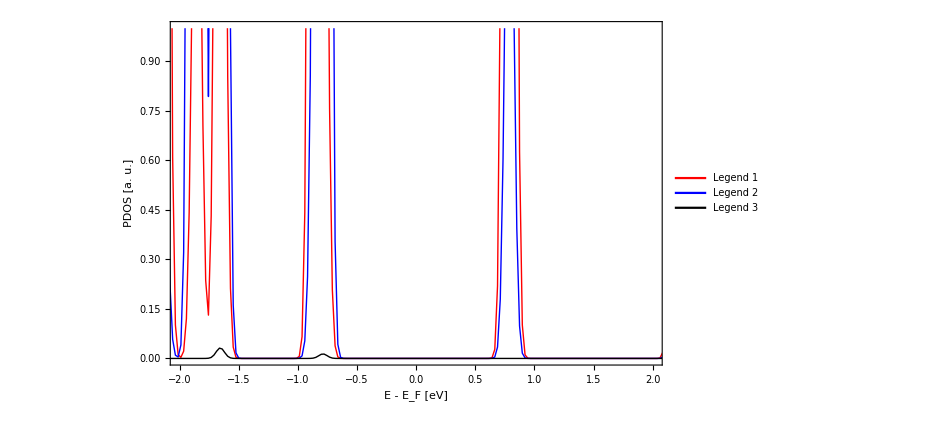

```mathematica
(* XY plot *)
jj=ListPlot[{dos1,dos2,dos3(*,dos4*)},Joined->True,PlotRange->{{-2,+2}(*{Automatic,Automatic}*),{0,1.0*10^0}},PlotStyle->styling (*AbsoluteThickness[4]*)(*Directive[Black,AbsoluteThickness[2]]*)(*{Thick,Thick,Directive[Thick,Dashed],Directive[Thick,Dashed]}*),Axes->{False,True},AxesStyle->AbsoluteThickness[2],AxesLabel->{,Style["Fermi Level",20,Black]},AxesOrigin->{0,0},Frame->True,FrameLabel->{"E - E_F [eV]"(*" E [eV]"*),"PDOS [a. u.]"},FrameStyle->Directive[Black,AbsoluteThickness[2],20],ImageSize->700,Filling->(*{1->0}*)None,FillingStyle->Directive[Darker[Gray,.3],Opacity[.5]],(*AspectRatio->1/4,*)PlotLegends->Placed[LineLegend[{"Legend 1","Legend 2","Legend 3","Legend 4","Legend 5","Legend 6".1c},LegendLabel->None(*"Legend:"*)(*"NEB image no.:"*),LabelStyle->{Darker[Gray,0.7],FontSize->32},LegendFunction->None],{0.75,0.75}]]
```

```mathematica
Export["~/Desktop/dos_af_3.pdf" (*path<>"dos.png"*),jj,Background->None]
```

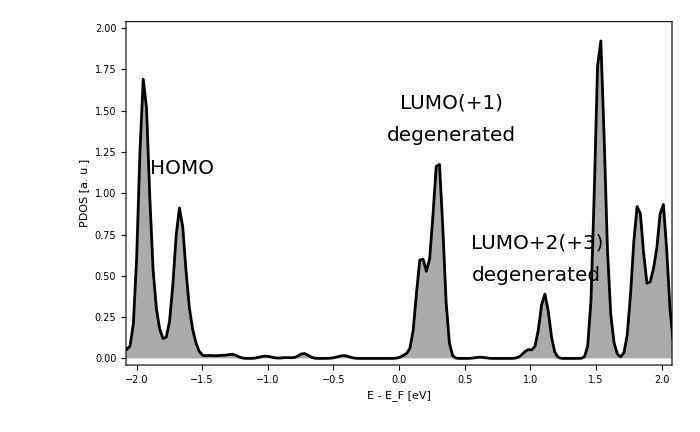

```mathematica
(* putting Text into the plot *)
jj2=Show[jj,Graphics[{Text[Style["HOMO",20],{-1.65,1.15}],Text[Style["LUMO(+1)",20],{0.4,1.55}],Text[Style["degenerated",20],{0.4,1.35}],Text[Style["LUMO+2(+3)",20],{1.05,0.7}],Text[Style["degenerated",20],{1.05,0.5}]}]]
```

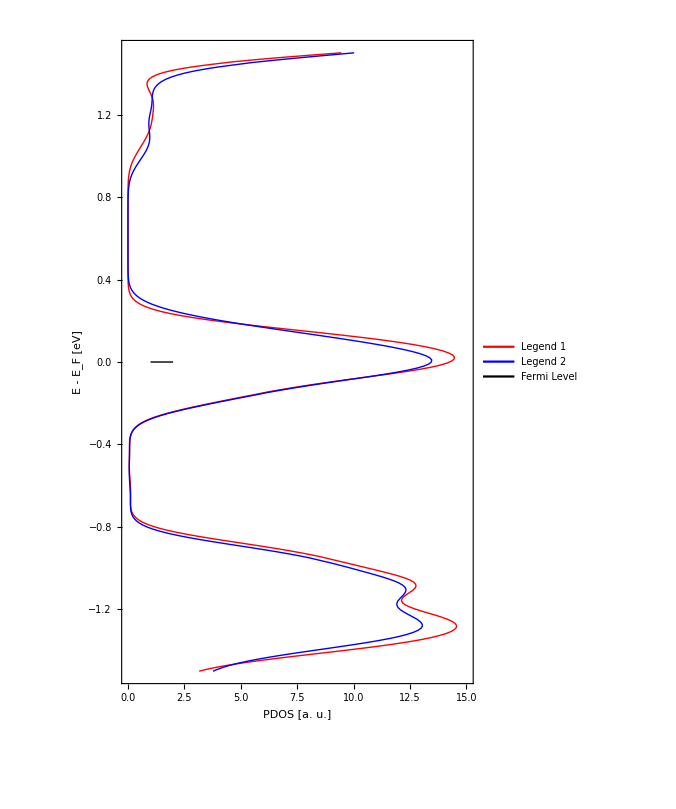

```mathematica
(* YX plot *)
jj=ListPlot[{dos2[[All,{2,1}]],dos1[[All,{2,1}]],{0,0}},Joined->True,PlotRange->{{0.02,1.5*10^1},{-1.5,+1.5}},PlotStyle->styling (*AbsoluteThickness[4]*)(*{Thick,Thick,Directive[Thick,Dashed],Directive[Thick,Dashed]}*),Axes->{True,False},AxesStyle->AbsoluteThickness[2],AxesLabel->(*{,Style["Fermi Level",20,Black]}*)None,AxesOrigin->{0,0},Frame->True,FrameLabel->{"PDOS [a. u.]"(*" E [eV]"*),"E - E_F [eV]"},FrameStyle->Directive[Black,AbsoluteThickness[2],20],ImageSize->500,AspectRatio->GoldenRatio,Filling->(*{1->0}*)None,FillingStyle->Directive[Orange,Opacity[.5]],PlotLegends->Placed[LineLegend[{"Legend 1","Legend 2","Fermi Level"},LegendLabel->None(*"Legend:"*)(*"NEB image no.:"*),LabelStyle->{Darker[Gray,0.7],FontSize->32},LegendFunction->None],{.5,.75}]]
```

```mathematica
Export["~/Desktop/dos_af_3.pdf" (*path<>"dos.png"*),jj,Background->None]
```

```mathematica
fillVertical[plot_,x0_: 0.]:=plot/.Line[p_]:>{{Opacity[0.5],Polygon[p~Join~{{N@x0,p[[-1,2]]},{N@x0,p[[1,2]]}}]},Line[p]}
```

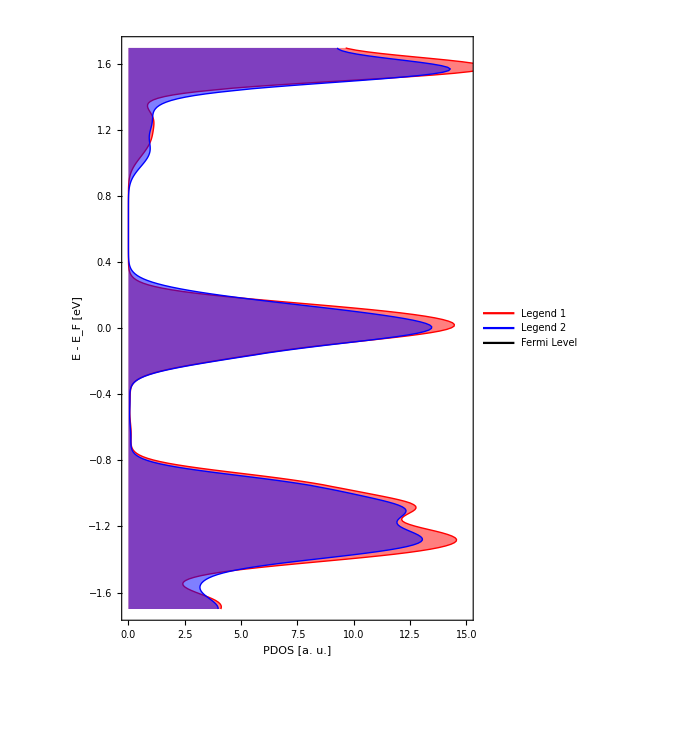

```mathematica
(* Filled YX plot *)
jj2=fillVertical[ListPlot[{dos2[[All,{2,1}]],dos1[[All,{2,1}]],{-30,-30}},Joined->True,PlotRange->{{0.00,1.5*10^1},{-1.7,+1.7}},PlotStyle->(*AbsoluteThickness[4]*)styling(*{Thick,Thick,Directive[Thick,Dashed],Directive[Thick,Dashed]}*),Axes->{True,False},AxesStyle->AbsoluteThickness[2],AxesLabel->(*{,Style["Fermi Level",20,Black]}*)None,AxesOrigin->{0,0},Frame->True,FrameLabel->{"PDOS [a. u.]"(*" E [eV]"*),"E - E_F [eV]"},FrameStyle->Directive[Black,AbsoluteThickness[2],32],ImageSize->500,AspectRatio->GoldenRatio-0.15,Filling->(*{1->0}*)None,FillingStyle->Directive[Orange,Opacity[.5]],PlotLegends->Placed[LineLegend[{"Legend 1","Legend 2","Fermi  Level"},LegendLabel->None(*"Legend:"*)(*"NEB image no.:"*),LabelStyle->{Darker[Gray,0.7],FontSize->32},LegendFunction->None],{.60,.73}]]]
```

```mathematica
Export["~/Desktop/dos_af_3.pdf",jj2,Background->None]
```

~/Desktop/dos_af_3.pdf

```mathematica
Export["~/Desktop/Fe_surf1_pdos.png",jj,Background->None]
```

~/Desktop/Fe_surf1_pdos.png

```mathematica
dos1=.;dos2=.;dos3=.;dos4=.;dos5=.;dos6=.;
```

## Single line plot & Mouse tracking

```mathematica
dosmol=Inner[Plus,Inner[Times,Import["~/Desktop/probe_particle_code/TOAT_old/TOAT/free_2/dens_TOT.dat"][[All,{1,2}]],{1,1},List],{(*+2.323*)0,0},List];
```

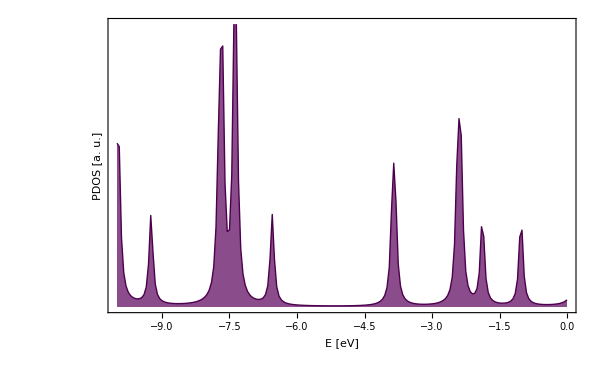

```mathematica
jj2=ListPlot[dosmol,Joined->True,PlotRange->{{-10,0}(*{Automatic,Automatic}*),{0,20}},PlotStyle->Directive[Thick,Darker[Purple,.4]],Axes->{False,True},AxesStyle->Directive[AbsoluteThickness[2],DotDashed],AxesLabel->{,Style["Fermi Level",20,Black]},AxesOrigin->{-5.302,0},Frame->True,FrameLabel->{(*"E - E_F [eV]"*)"E [eV]","PDOS [a. u.]"},FrameStyle->Directive[Black,AbsoluteThickness[2],20],ImageSize->600,Filling->{1->0}(*None*),FillingStyle->Directive[Darker[Purple,.3],Opacity[.7]],FrameTicks->{Automatic,None}(*,PlotLegends->Placed[LineLegend[{"Si substrate","molecule"},LegendLabel->None(*"Legend:"*)(*"NEB image no.:"*),LabelStyle->{Darker[Gray,0.7],FontSize->32},LegendFunction->None],{.66,.69}]*)]
```

```mathematica
Export["~/Desktop/dens_mol.pdf",jj2,Background->None]
```

```mathematica
(* Mouse tracking *)
```

```mathematica
{-Graphics-,Dynamic[MousePosition["Graphics"]]}
```

{-Graphics-,}

## View

```mathematica
atomicprop=Import[NotebookDirectory[]<>"/atomic_prop.dat","Table"];
path="~/Documents/WORK/z-sshfs/tmp/VASP/";
filename="CONTCAR"; (* "bas","xyz","in" and CONTCAR/POSCAR files are supported at the moment *)
geomin= Import[path<>filename,"Table"];
geomin[[Range[1,20]]]//TableForm (* Just to see an example *)
```

~/Documents/WORK/z-sshfs/tmp/Fireball/

```mathematica
(* geometry parser *)
If[StringTake[filename,-3]=="bas",{Print["BAS file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=2,i≤maxat1+1,i++,geom[[i-1]]={geomin[[i,1]],atomicprop[[geomin[[i,1]],1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[geomin[[i,1]],2]],atomicprop[[geomin[[i,1]],4]],atomicprop[[geomin[[i,1]],5]],atomicprop[[geomin[[i,1]],6]];}];};,
If[StringTake[filename,-3]=="xyz",{Print["XYZ file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=3,i≤maxat1+2,i++,For[j=1,j≤99,j++,If[ToString[geomin[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i-2]]={j,geomin[[i,1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]==".in",{Print["FHI-AIMS in file"];aimsimport2=Array[Null,Length[geomin]];ia=1;cell={};
For[i=1,i≤Length[aimsimport2],i++,If[geomin[[i,1]]=="atom",{aimsimport2[[ia]]=geomin[[i]],ia=ia+1},If[geomin[[i,1]]=="lattice_vector",cell=Append[cell,geomin[[i,{2,3,4}]]]]]];
aimsimport2=Drop[aimsimport2,-Length[geomin]+ia-1];If[cell=={},cell=.];
xyzEx=aimsimport2[[All,{5,2,3,4}]];(*geomin=.;*)aimsimport2=.;
maxat1=Length[xyzEx];
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,For[j=1,j≤Length[atomicprop],j++,If[ToString[xyzEx[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i]]={j,xyzEx[[i,1]],xyzEx[[i,2]],xyzEx[[i,3]],xyzEx[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]=="CAR",{Print["CONTCAR/POSCAR VASP file"],(*VASP CONTCAR file *)direct=False;
If[geomin[[8,1]]=="Direct",{Print[".1dOK"],tmpn=8,direct=True},If[geomin[[9,1]]=="Direct",{Print[".1dOK"],tmpn=9,direct=True},
If[geomin[[8,1]]=="Cartesian",{Print[".1dOK"],tmpn=8},If[geomin[[9,1]]=="Cartesian",{Print[".1dOK"],tmpn=9},
{Print["problem: geomin[[8,1] = "]<>geomin[[8,1]],Print["problem: geomin[[9,1] = "]<>geomin[[9,1]]}]]]];
tmpn;cell=geomin[[{3,4,5}]];elem=geomin[[6]];
elnum=Length[elem];elemdic=Table[,{i,elnum}];atnum=geomin[[7]];
maxat1=Sum[atnum[[i]],{i,elnum}];atsum=Table[Sum[atnum[[i]],{i,j}],{j,1,elnum}];
For[i=1,i≤elnum,i++,For[j=1,j≤99,j++,If[ToString[elem[[i]]]==ToString[atomicprop[[j,1]]],elemdic[[i]]=j]]];elemdic;
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,{For[j=1,j≤elnum,j++,If[i≤atsum[[j]],{tmp=j,Break[]}]],k=elemdic[[tmp]],geom[[i]]={k,elem[[tmp]],geomin[[i+tmpn,1]],geomin[[i+tmpn,2]],geomin[[i+tmpn,3]],atomicprop[[k,2]],atomicprop[[k,4]],atomicprop[[k,5]],atomicprop[[k,6]]};};];
If[direct,geom[[All,{3,4,5}]]=geom[[All,{3,4,5}]].cell];},{Print["Unknown Format"]}]]]].1c
```

```mathematica
(* CONTINUATION of geometry reading and plotting *)
rescale = 0.2;
balls=Table[Tooltip[{RGBColor[geom[[i,{7,8,9}]]/256],Sphere[geom[[i,{3,4,5}]],rescale*geom[[i,6]]]},{i,geom[[i,{2,3,4,5}]]}],{i,1,maxat1}];
resbond=1.2;bond=.1;

geom2 = Array[Null, {(maxat1^2), 12}];
k1 = 1;
For[i = 1, i ≤maxat1 , i++, For[j = 1, j < i, j++, If[Norm[geom[[i,{3,4,5}]]-geom[[j,{3,4,5}]]]<= (atomicprop[[geom[[i, 1]], 3]]*resbond + atomicprop[[geom[[j, 1]], 3]]*resbond), {geom2[[k1, {1,2,3,7,8,9}]] =geom[[i,{ 3,4,5,7,8,9}]], geom2[[k1, {4,5,6,10,11,12}]] =geom[[j,{ 3,4,5,7,8,9}]], k1 = k1 + 1}]]];
geom2=Drop[geom2,k1-1-(maxat1^2)];
sticks=Table[Tube[{geom2[[i,{1,2,3}]],geom2[[i,{4,5,6}]]},bond,VertexColors->{RGBColor[geom2[[i,{7,8,9}]]/256],RGBColor[geom2[[i,{10,11,12}]]/256]}],{i,1,Length[geom2],1}];
```

```mathematica
Graphics3D[{balls,sticks},Lighting->"Neutral",ViewPoint->20000. {0,-1,0.1},ImageSize-> 300,Axes->False,Boxed-> False,Background->None]
```

-Graphics3D-

Use only one of the following cells according to used format

```mathematica
(* FHI-AIMS PDOS *)
shift=0.0;
list=Table[i,{i,1,maxat1,1}];
path0=path;
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];
dos1=Import[path0<>"atom_projected_dos_"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4][[All,{1,2}]];dos1[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<10,Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_projected_dos_"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4]]]},{i,list}];
dos1[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{doses[i]=dd[i][[All,2]],dd[i]=.},{i,list}];tmp1=.;
dos1=Inner[Plus,dos1,{shift,0},List];
```

```mathematica
(* VASP PDOS *)
shift=0.0;
list=Table[i,{i,1,maxat1,1}];
pathse=path;
doscar1=Import[pathse<>"DOSCAR","Table"];
doscar1[[Range[1,7]]];noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]];
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.;
For[i=1,i≤noat,i++,{doses[i]=dos01[i].{0,1,1,1},dos01[i]=.}]; (* spd division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{doses[i]=dos01[i].{0,1,1,1,1,1,1,1,1,1},dos01[i]=.}];*) (* spxpy... division LORBIT=11*)
dosesmol=Array[Null,{nosteps,2}];dosesmol[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmol[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmol[[i,2]]=dosesmol[[i,2]]+doses[list[[j]]][[i]]]}];
dos1=Inner[Plus,dosesmol,{-fermi+shift,0},List];
```

```mathematica
(* Fireball PDOS *)
shift=0.0;
list=Table[i,{i,1,maxat1,1}];
path0=path;
dos1=Import[path0<>"dens_0001.dat","Table"][[All,{1,2}]];dos1[[All,2]]=0;
Do[{dd[i]=If[i≥100,Import[path0<>"dens_0"<>ToString[i]<>".dat","Table"],If[i<10,Import[path0<>"dens_000"<>ToString[i]<>".dat","Table"],Import[path0<>"dens_00"<>ToString[i]<>".dat","Table"]]]},{i,list}];dos1[[All,2]]=Sum[dd[i][[All,Dimensions[dd[i]][[2]]-1]],{i,list}];Do[{doses[i]=dd[i][[All,Dimensions[dd[i]][[2]]-1]],dd[i]=.},{i,list}];f=Import[path0<>"fermi.dat","Table"][[1,4]];dos1=Inner[Plus,dos1,{-f+shift,0},List];f=.;
```

```mathematica
(* GPAW PDOS *)
list=Table[i,{i,1,maxat1,1}];
path0=path;
dos1=Import[path0<>"pdos_1.dat","Table"][[All,{1,2}]];dos1[[All,2]]=0;
Do[{dd[i]=Import[path0<>"pdos_"<>ToString[i-1]<>".dat","Table"]},{i,list}];dos1[[All,2]]=Sum[dd[i][[All,2]],{i,list}];Do[{doses[i]=dd[i][[All,2]],dd[i]=.},{i,list}];
```

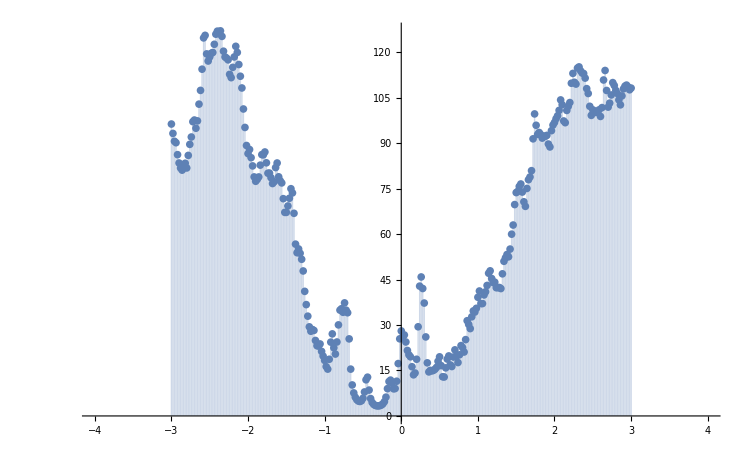

```mathematica
ListPlot[Table[Tooltip[dos1[[i]],i],{i,1,Length[dos1]}],Filling->Axis,Joined->False,PlotRange->{{-4,4},{0,Max[dos1[[All,2]]]}},ImageSize->750]
```

```mathematica
first=111;
last=116;
max=0.0;
For[i=1,i≤maxat1,i++,{dosessum[i]=Total[doses[i][[Range[first,last,1]]]],If[dosessum[i]>max,max=dosessum[i]]}];
max
For[i=1,i≤maxat1,i++,{dosessum[i]=dosessum[i]/max}]

rescale2 = 0.4;
color=(*"TemperatureMap"*)"DarkRainbow";
With[{c=ColorData[color]},
geom03=Table[{Opacity[dosessum[i]],(*Darker[Blue,.3]*)c[dosessum[i]],Sphere[geom[[i,{3,4,5}]],rescale2*geom[[i,6]]]},{i,1,maxat1}]];
expo=Graphics3D[{geom03,balls,sticks},Lighting->"Neutral",ViewPoint->20000. {0,-1,1},ImageSize->1000,Axes->False,Boxed-> False,Background->None]
```

14.6428

-Graphics3D-

```mathematica
Export[path<>"-1.5_state.png",expo,Background->None]
```

Desktop/-4_state.png

```mathematica
expo=.
```

```mathematica
Do[{dosessum[i]=.;doses[i]=.},{i,maxat1}]
```

## Older repository

```mathematica
(* BAS file *)
maxat1=geomin[[1,1]](*108+17+14*);
geom=Array[Null,{maxat1+1,9}];
For[i=2,i≤maxat1+1,i++,geom[[i-1]]={geomin[[i,1]],atomicprop[[geomin[[i,1]],1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[geomin[[i,1]],2]],atomicprop[[geomin[[i,1]],4]],atomicprop[[geomin[[i,1]],5]],atomicprop[[geomin[[i,1]],6]]}]
```

```mathematica
(* XYZ file *)
maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=3,i≤maxat1+2,i++,For[j=1,j≤99,j++,If[ToString[geomin[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i-2]]={j,geomin[[i,1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]}]]]
```

```mathematica
(* FHI-AIMS in file *)
aimsimport2=Array[Null,Length[geomin]];ia=1;
For[i=1,i≤Length[aimsimport2],i++,If[geomin[[i,1]]=="atom",{aimsimport2[[ia]]=geomin[[i]],ia=ia+1}]];
aimsimport2=Drop[aimsimport2,-Length[geomin]+ia-1];
xyzEx=aimsimport2[[All,{5,2,3,4}]];(*geomin=.;aimsimport2=.;*)
maxat1=Length[xyzEx]
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,For[j=1,j≤Length[atomicprop],j++,If[ToString[xyzEx[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i]]={j,xyzEx[[i,1]],xyzEx[[i,2]],xyzEx[[i,3]],xyzEx[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]}]]]
```

57

```mathematica
(*VASP CONTCAR file *)
If[geomin[[8,1]]=="Direct",{Print[".1dOK"],tmpn=8},If[geomin[[9,1]]=="Direct",{Print[".1dOK"],tmpn=9},{Print["problem: geomin[[8,1] = "]<>geomin[[8,1]],Print["problem: geomin[[9,1] = "]<>geomin[[9,1]]}]];
tmpn
cell=geomin[[{3,4,5}]];elem=geomin[[6]];
elnum=Length[elem];elemdic=Table[,{i,elnum}];atnum=geomin[[7]];
maxat1=Sum[atnum[[i]],{i,elnum}];atsum=Table[Sum[atnum[[i]],{i,j}],{j,1,elnum}];
For[i=1,i≤elnum,i++,For[j=1,j≤99,j++,If[ToString[elem[[i]]]==ToString[atomicprop[[j,1]]],elemdic[[i]]=j]]];elemdic;
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,{For[j=1,j≤elnum,j++,If[i≤atsum[[j]],{tmp=j,Break[]}]],k=elemdic[[tmp]],geom[[i]]={k,elem[[tmp]],geomin[[i+tmpn,1]],geomin[[i+tmpn,2]],geomin[[i+tmpn,3]],atomicprop[[k,2]],atomicprop[[k,4]],atomicprop[[k,5]],atomicprop[[k,6]]}}]
geom[[All,{3,4,5}]]=geom[[All,{3,4,5}]].cell;
```

.1dOK

9